```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];Get["HopfE`"];
(*Two-Strain Model with Saturation*)RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"->0,"i1"->0,"i2"->0};
rts={La,be1*s*i1,be2*s*i2,μ*s,(μ +ga1)*i1,(μ+ga2)*i2};
rtsP=rts*{1,1/(1+a1*i1),1/(1+a2*i2),1,1,1};
Print["reactions and transitions: ",Transpose[{RN,rtsP}]//MatrixForm]
(*Get bdAn outputs*)
{RHS,var,par, cp,mSi,Jx,Jy,E0,ngm,R0,R0A,EA,E1t,E2t} = bdAn[RN, rtsP];
Print["R1,R2 are"]
{R01,R02}=R0A/.E0
```

reactions and transitions: (0→s | La
i1+s→2 i1 | (be1 i1 s)/(1+a1 i1)
i2+s→2 i2 | (be2 i2 s)/(1+a2 i2)
s→0 | s μ
i1→0 | i1 (ga1+μ)
i2→0 | i2 (ga2+μ))

RHS=(La-(be1 i1 s)/(1+a1 i1)-(be2 i2 s)/(1+a2 i2)-s μ
(be1 i1 s)/(1+a1 i1)-i1 (ga1+μ)
(be2 i2 s)/(1+a2 i2)-i2 (ga2+μ)) has var {s,i1,i2} par{a1,a2,be1,be2,ga1,ga2,La,μ}

minimal siphons {{i1},{i2}} and invasion species are at positions: {2,3}

DFE solution E0: {s→La/μ,i1→0,i2→0}

NGM K= ((be1 s)/(ga1+μ) | 0
0 | (be2 s)/(ga2+μ))

Eigenvalues: {(be2 s)/(ga2+μ),(be1 s)/(ga1+μ)}

Eigenvectors: {{0,1},{1,0}}

Nonzero eigenvalues: {(be2 s)/(ga2+μ),(be1 s)/(ga1+μ)}

Strain positions in NGM space - strain 1: {1}, strain 2: {2}

Processing eigenvalue 1 with eigenvector: {0,1}

Strain 1 nonzero components = 0, Strain 2 nonzero components = 1

Processing eigenvalue 2 with eigenvector: {1,0}

Strain 1 nonzero components = 1, Strain 2 nonzero components = 0

Strain associations: {2,1}

Ordered reproduction functions R0A: {(be1 s)/(ga1+μ),(be2 s)/(ga2+μ)}

R0A[[1]] (strain 1): (be1 s)/(ga1+μ)

R0A[[2]] (strain 2): (be2 s)/(ga2+μ)

Number of boundary systems= 2; first sys has 2 sols, second sys has 2 sols

E1t solutions:

1: {i1→0,s→La/μ}

2: {i1→-(-be1 La+ga1 μ+μ^2)/((ga1+μ) (be1+a1 μ)),s→(ga1+a1 La+μ)/(be1+a1 μ)}

E2t solutions:

1: {i2→0,s→La/μ}

2: {i2→-(-be2 La+ga2 μ+μ^2)/((ga2+μ) (be2+a2 μ)),s→(ga2+a2 La+μ)/(be2+a2 μ)}

R1,R2 are

{(be1 La)/(μ (ga1+μ)),(be2 La)/(μ (ga2+μ))}

```mathematica
{E1,E2,R12,R21,coP}=invNr[E1t,E2t,R0A,E0,par,cp,2,2]
```

Selected E1 (solution 2): {i1→-(-be1 La+ga1 μ+μ^2)/((ga1+μ) (be1+a1 μ)),s→(ga1+a1 La+μ)/(be1+a1 μ)}

Selected E2 (solution 2): {i2→-(-be2 La+ga2 μ+μ^2)/((ga2+μ) (be2+a2 μ)),s→(ga2+a2 La+μ)/(be2+a2 μ)}

invasion numbers are{(be2 (ga1+a1 La+μ))/((ga2+μ) (be1+a1 μ)),(be1 (ga2+a2 La+μ))/((ga1+μ) (be2+a2 μ))}

under coP: {a1→3,a2→1,be1→4,be2→3,ga1→1,ga2→1,La→1,μ→1} invasion nrs are{1.07143,1.5} repr nrs are{2.,1.5}

END invNr OUTPUT

{{i1→-(-be1 La+ga1 μ+μ^2)/((ga1+μ) (be1+a1 μ)),s→(ga1+a1 La+μ)/(be1+a1 μ)},{i2→-(-be2 La+ga2 μ+μ^2)/((ga2+μ) (be2+a2 μ)),s→(ga2+a2 La+μ)/(be2+a2 μ)},(be2 (ga1+a1 La+μ))/((ga2+μ) (be1+a1 μ)),(be1 (ga2+a2 La+μ))/((ga1+μ) (be2+a2 μ)),{a1→3,a2→1,be1→4,be2→3,ga1→1,ga2→1,La→1,μ→1}}

```mathematica
eq=Thread[(RHS/.coP)==0];
so=Solve[eq,var]//FullSimplify;
Print[so//Length," sols at nr. col coP, one is positive",so//N]
p0val=par/.coP;
pos=fpHopf[RHS, var, par, p0val]
```

4 sols at nr. col coP, one is positive{{s→1.,i1→0.,i2→0.},{s→0.6875,i1→0.125,i2→0.03125},{s→0.714286,i1→0.142857,i2→0.},{s→0.75,i1→0.,i2→0.125}}

{{{0.6875,0.125,0.03125}},{-0.966025+0.662008 ⅈ,-0.966025-0.662008 ⅈ},-55.5775,{-0.966025+0.662008 ⅈ,-0.966025-0.662008 ⅈ,-0.128555}}

Auto-determined varInd: {1,2,3}

Susceptible: s

Strain 1 (first compartment): i1

Strain 2 (first compartment): i2

Checked 1135 potential coexistence points

All Rij equations: {be1/2==1,be2/2==1,(5 be2)/(2 (3+be1))==1,(3 be1)/(2 (1+be2))==1}

DFE: 400 (8%)

E2: 1333 (28%)

E1: 1932 (40%)

EE-Stable: 1135 (24%)

{20.7656,Null}

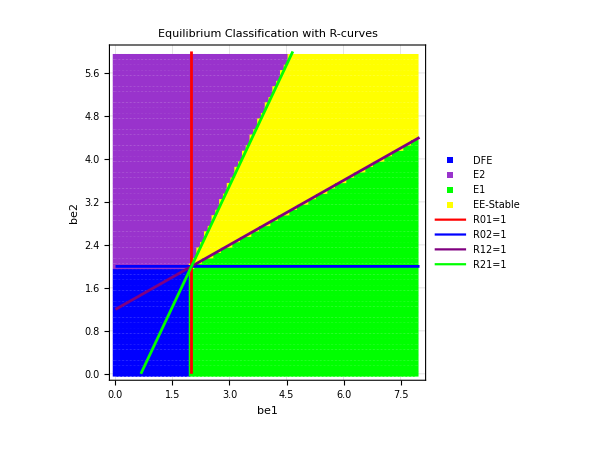

```mathematica
plotInd={3,4};
steTol=10^(-8);
staTol=10^(-10);
choTol=10^(-13);

(*Call scan using all the precomputed values from memory*)
Timing[{fPl,unC,res}=scan[RHS,var,par,coP,plotInd,mSi,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]

fPl
```

```mathematica
Export["RahmanScan.pdf",fPl]
```

RahmanScan.pdf

```mathematica
Clear[scan4TS]

(*Simplified Time Series Simulation-based multiple equilibrium scanning*)
scan4TS[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic,tMax_:100,nInitials_:8,steadyTol_:10^(-6)]:=Block[{bifP1,bifP2,bifP1min,bifP1max,bifP2min,bifP2max,stepSize,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,betterColors,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,R01F,R02F,R21F,R12F,rCurves,coPForR,numpar,conPar,initialConditions,tsol,finalValues,I1val,I2val,tol,currentType,allSols,uniqueSols,eqType,eqTypes,steadyStateReached,lastValues,deltaCheck,icSet,ic,finalTime,pos,rhsWithParams,rhsWithFunctions,odeSystem,initialCondSystem,I1Index,I2Index,solTol},(*Define colors*)betterColors={RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[0.8,0.5,0.2],RGBColor[0.6,0.3,0.8],RGBColor[1,1,0],RGBColor[1,0.5,0],RGBColor[0,0.8,0.8],RGBColor[0.8,0,0.8],RGBColor[0.5,0.8,0.5],RGBColor[0.8,0.8,0.5],RGBColor[1.0,0.0,1.0]};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract bifurcation parameter indices*)bifParIdx1=First[plotInd];
bifParIdx2=Last[plotInd];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
If[useGridMode,(*GRID MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];,(*RANGE MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}];];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
(*Initialize for time series scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);
(*Create diverse initial condition sets*)initialConditions={};
(*Set 1:DFE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 2:E1-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 3:E2-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Set 4:EE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Additional random initial conditions*)Do[icSet=Table[RandomReal[{0.001,0.2}],{Length[var]}];
AppendTo[initialConditions,icSet];,{nInitials-4}];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Substitute parameters in RHS*)rhsWithParams=RHS/. conPar;
rhsWithFunctions=rhsWithParams/. Thread[var->Through[var[t]]];
(*Run time series from different initial conditions*)allSols={};
Do[ic=initialConditions[[k]];
odeSystem=MapThread[#1'[t]==#2&,{var,rhsWithFunctions}];
initialCondSystem=MapThread[#1[0]==#2&,{var,ic}];
tsol=Quiet[NDSolve[Join[odeSystem,initialCondSystem],var,{t,0,tMax}]];
If[Length[tsol]>0&&tsol[[1]]=!=$Failed,finalValues=Table[var[[j]][tMax]/. tsol[[1]],{j,1,Length[var]}];
finalTime=0.9*tMax;
lastValues=Table[var[[j]][finalTime]/. tsol[[1]],{j,1,Length[var]}];
deltaCheck=Max[Abs[finalValues-lastValues]];
steadyStateReached=(deltaCheck<steadyTol);
If[steadyStateReached&&AllTrue[finalValues,#>=0&],AppendTo[allSols,finalValues]];];,{k,1,Length[initialConditions]}];
If[Length[allSols]>0,(*Find unique attractors*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify equilibria*)If[Length[uniqueSols]>1,eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
eqTypes=Sort[DeleteDuplicates[eqTypes]];
currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",True,"Multiple"];,(*Single attractor*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[bifP1],N[bifP2],currentType}];,(*No solutions found*)res=Append[res,{N[bifP1],N[bifP2],"NotGAS"}];];,{bifP2,bifP2vals}];,{bifP1,bifP1vals}];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
(*Create simple plot*)plotData=Table[Select[res,#[[3]]==outcomes[[i]]&][[All,1;;2]],{i,1,Length[outcomes]}];
finalPlot=ListPlot[plotData,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->outcomes,AspectRatio->1,PlotRange->{{bifP1min,bifP1max},{bifP2min,bifP2max}}];
(*Add original plot if provided*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot]];
(*Simple summary*)Do[Print[outcomes[[i]],": ",outcomeCounts[[i]]," (",Round[100.*outcomeCounts[[i]]/Length[res]],"%)"],{i,1,Length[outcomes]}];
(*Return NotGAS points as errors*)unClassifPoints=Select[res,#[[3]]=="NotGAS"&];
{finalPlot,unClassifPoints,res}];
```

DFE: 42 (3%)

NotGAS: 211 (17%)

E2: 341 (28%)

E1: 440 (36%)

EE: 191 (16%)

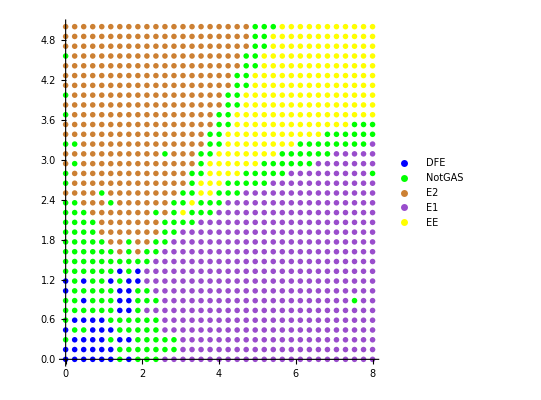

```mathematica
plotInd={1,2};
{fPl,noS,res}=scan4TS[RHS,var,par,p0val,plotInd,35,Automatic,0.01,1/20,1.0,1.0,R01,R02,R21,R12,100,8,10^(-6)];fPl
```

DFE: 48 (4%)

NotGAS: 149 (12%)

E2: 356 (29%)

E1: 453 (37%)

EE: 219 (18%)

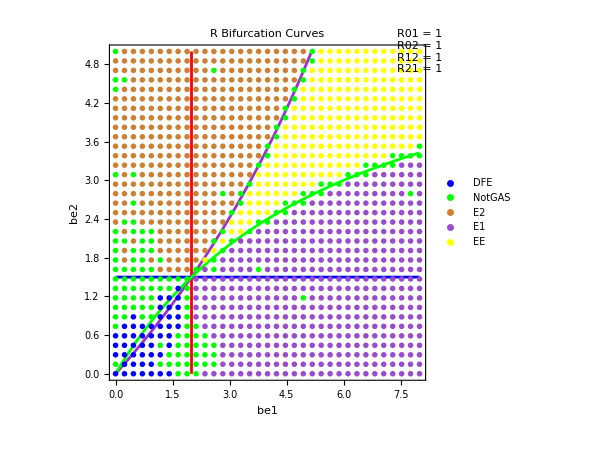

```mathematica
tMax=200;nIc=8;{fPl,noS,res}=scan4TS[RHS,var,par,p0val,plotInd,35,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12,tMax,nIc,10^(-6)];fPl
```

I1 at index 2, I2 at index 5

Varying parameters at indices {1,2} with center values: {4,5/2}

Using grid mode with 60×60 points...

Total points to scan: 3600

Initial conditions created

Scanning complete!

Found equilibrium types: {DFE (270 points),E2 (919 points),E1 (1291 points),EE (236 points),E1-E2 (344 points),error (18 points),EE-E2 (88 points),EE-E1 (213 points),Coexist (221 points)}

Including 18 errors

Summary:

DFE | 270 | 8%
E2 | 919 | 26%
E1 | 1291 | 36%
EE | 236 | 7%
E1-E2 | 344 | 10%
error | 18 | 0%
EE-E2 | 88 | 2%
EE-E1 | 213 | 6%
Coexist | 221 | 6%

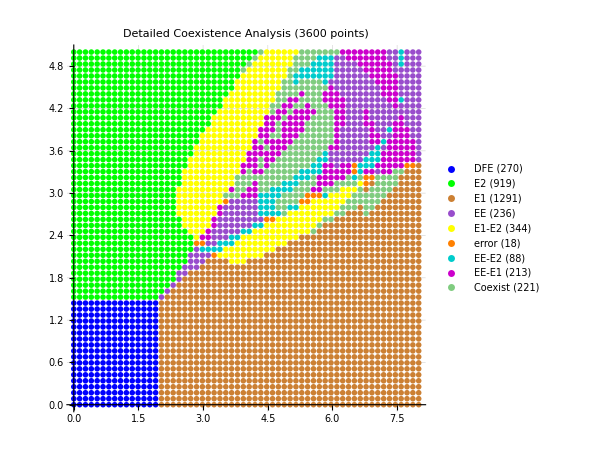

Varying be1 (center=4) and be2 (center=5/2)

Ranges: be1 ∈ {0.,8.}, be2 ∈ {0.,5.}

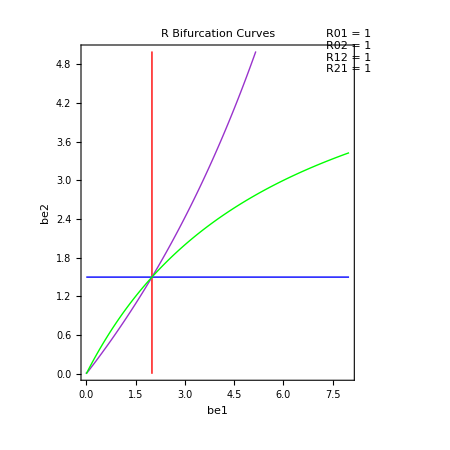

```mathematica
(*Multiple equilibrium scanning with coexistence detection*)scan4[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic]:=Module[{(*Parameter ranges and scanning*)β1,β2,β1min,β1max,β2min,β2max,stepSize,β1vals,β2vals,totalPoints,(*Results collection*)res,outcomes,outcomeCounts,(*Plotting and visualization*)finalPlot,plotData,betterColors,simpleTooltips,(*Mode detection*)useGridMode,β1Index,β2Index,β1Center,β2Center,(*Progress tracking*)progressVar,currentProgress,(*R curve variables*)R01F,R02F,R21F,R12F,rCurves,coPForR,(*Multiple equilibrium variables*)numpar,conPar,inP,in0,in1,in2,sol0,sol1,sol2,solMain,I1val,I2val,tol,currentType,errors,gridResults,nB1,nB2,(*Index finding*)I1Index,I2Index,solTol,allSols,uniqueSols,eqType,eqTypes},(*Define colors including detailed coexistence categories*)betterColors={RGBColor[0,0,1],(*Pure Blue for DFE*)RGBColor[0,1,0],(*Pure Green for E1*)RGBColor[0.8,0.5,0.2],(*Orange for E2*)RGBColor[0.6,0.3,0.8],(*Purple for EE*)RGBColor[1,1,0],(*Yellow for EE-E1*)RGBColor[1,0.5,0],(*Red-Orange for EE-E2*)RGBColor[0,0.8,0.8],(*Cyan for E1-E2*)RGBColor[0.8,0,0.8],(*Magenta for EE-DFE*)RGBColor[0.5,0.8,0.5],(*Light Green for E1-DFE*)RGBColor[0.8,0.8,0.5],(*Light Orange for E2-DFE*)RGBColor[1.0,0.0,1.0](*Magenta for errors/NoSol*)};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
Print["I1 at index ",I1Index,", I2 at index ",I2Index];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract parameter indices*)β1Index=If[Length[plotInd]>=1,plotInd[[1]],1];
β2Index=If[Length[plotInd]>=2,plotInd[[2]],2];
β1Center=p0val[[β1Index]];
β2Center=p0val[[β2Index]];
Print["Varying parameters at indices ",{β1Index,β2Index}," with center values: ",{β1Center,β2Center}];
If[useGridMode,(*GRID MODE*)Print["Using grid mode with ",gridRes,"×",gridRes," points..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1min+(β1max-β1min)*k/(gridRes-1),{k,0,gridRes-1}];
β2vals=Table[β2min+(β2max-β2min)*k/(gridRes-1),{k,0,gridRes-1}];
stepSize="grid";,(*RANGE MODE*)Print["Using range mode with step size ",delta,"..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1,{β1,β1min,β1max,delta}];
β2vals=Table[β2,{β2,β2min,β2max,delta}];
stepSize=delta;];
(*R curve preparation*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R21=!=Automatic||R12=!=Automatic,coPForR=Thread[par->p0val];
coPForR=DeleteCases[coPForR,HoldPattern[par[[β1Index]]->_]|HoldPattern[par[[β2Index]]->_]];
If[R01=!=Automatic,R01F=R01/. coPForR;
AppendTo[rCurves,ContourPlot[R01F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Red,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R02=!=Automatic,R02F=R02/. coPForR;
AppendTo[rCurves,ContourPlot[R02F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Blue,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R21=!=Automatic,R21F=R21/. coPForR;
AppendTo[rCurves,ContourPlot[R21F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Green,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R12=!=Automatic,R12F=R12/. coPForR;
AppendTo[rCurves,ContourPlot[R12F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Orange,Thick,Opacity[0.8]],PlotPoints->30]]];];
totalPoints=Length[β1vals]*Length[β2vals];
Print["Total points to scan: ",totalPoints];
(*Initialize for multiple equilibrium scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);(*Tolerance for comparing solutions*)(*Create initial condition arrays*)inP=Table[{var[[j]],1/Length[var]},{j,Length[var]}];(*General initial*)in0=inP;in0[[I1Index,2]]=0;in0[[I2Index,2]]=0;(*DFE:I1=I2=0*)in1=inP;in1[[I2Index,2]]=0;(*E1:I2=0*)in2=inP;in2[[I1Index,2]]=0;(*E2:I1=0*)Print["Initial conditions created"];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP WITH 4 EQUILIBRIUM SEARCHES*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[β1Index]]=β1;
numpar[[β2Index]]=β2;
conPar=Thread[par->numpar];
(*Four FindRoot calls with different initial conditions*)solMain=Quiet[FindRoot[RHS/. conPar,inP]];(*General*)sol0=Quiet[FindRoot[RHS/. conPar,in0]];(*DFE-like*)sol1=Quiet[FindRoot[RHS/. conPar,in1]];(*E1-like*)sol2=Quiet[FindRoot[RHS/. conPar,in2]];(*E2-like*)(*Collect all successful solutions*)allSols={};
If[Head[solMain]===List,AppendTo[allSols,var/. solMain]];
If[Head[sol0]===List,AppendTo[allSols,var/. sol0]];
If[Head[sol1]===List,AppendTo[allSols,var/. sol1]];
If[Head[sol2]===List,AppendTo[allSols,var/. sol2]];
If[Length[allSols]>0,(*Find unique solutions (within tolerance)*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify based on number of unique equilibria*)If[Length[uniqueSols]>1,(*Multiple equilibria-classify each and determine coexistence type*)eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
(*Remove duplicates and sort to get consistent naming*)eqTypes=Sort[DeleteDuplicates[eqTypes]];
(*Determine coexistence type*)currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",ContainsAll[eqTypes,{"EE","DFE"}]&&Length[eqTypes]==2,"EE-DFE",ContainsAll[eqTypes,{"E1","DFE"}]&&Length[eqTypes]==2,"E1-DFE",ContainsAll[eqTypes,{"E2","DFE"}]&&Length[eqTypes]==2,"E2-DFE",True,"Coexist" (*For 3+types or unexpected combinations*)];,(*Single equilibrium-classify by I1,I2 values*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[β1],N[β2],currentType}];,(*All FindRoot calls failed*)res=Append[res,{N[β1],N[β2],"NoSol"}];];,{β2,β2vals}];,{β1,β1vals}];
Print["Scanning complete!"];
(*Simple error detection for grid mode*)errors={};
If[useGridMode&&gridRes>2,gridResults=Table[Table[Null,{j,1,gridRes}],{i,1,gridRes}];
Do[Do[pos=Position[res,{β1vals[[i]],β2vals[[j]],_}];
If[Length[pos]>0,gridResults[[i,j]]=res[[pos[[1,1]],3]]];,{j,1,gridRes}];,{i,1,gridRes}];
Do[Do[If[gridResults[[i,j]]=!=Null,neighbors={};
If[i>1,AppendTo[neighbors,gridResults[[i-1,j]]]];
If[i<gridRes,AppendTo[neighbors,gridResults[[i+1,j]]]];
If[j>1,AppendTo[neighbors,gridResults[[i,j-1]]]];
If[j<gridRes,AppendTo[neighbors,gridResults[[i,j+1]]]];
neighbors=DeleteCases[neighbors,Null];
If[Length[neighbors]>=3&&Length[DeleteDuplicates[Join[{gridResults[[i,j]]},neighbors]]]>=4,AppendTo[errors,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
pos=Position[res,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
If[Length[pos]>0,res[[pos[[1,1]],3]]="error"];];];,{j,2,gridRes-1}];,{i,2,gridRes-1}];];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
Print["Found equilibrium types: ",Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>" points)",{i,1,Length[outcomes]}]];
Print["Including ",Length[errors]," errors"];
(*Create plot*)simpleTooltips=Table[Table[If[res[[j,3]]==outcomes[[i]],Tooltip[res[[j,1;;2]],outcomes[[i]]<>": β1="<>ToString[Round[res[[j,1]],0.01]]<>", β2="<>ToString[Round[res[[j,2]],0.01]]],Nothing],{j,1,Length[res]}],{i,1,Length[outcomes]}];
finalPlot=ListPlot[simpleTooltips,GridLines->Automatic,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>")",{i,1,Length[outcomes]}],AspectRatio->1,PlotLabel->"Detailed Coexistence Analysis ("<>ToString[Length[res]]<>" points)",FrameLabel->{"Parameter "<>ToString[β1Index],"Parameter "<>ToString[β2Index]},LabelStyle->{FontSize->12,Black},ImageSize->450,PlotRange->{{β1min,β1max},{β2min,β2max}}];
(*Add R curves and overlays*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot,Sequence@@rCurves,Graphics[{EdgeForm[{Thick,Gray,Dashed}],FaceForm[None],Rectangle[{β1min,β2min},{β1max,β2max}],Blue,PointSize[0.015],Point[{{β1Center,β2Center}}]}],PlotRange->{{β1min*0.9,β1max*1.1},{β2min*0.9,β2max*1.1}}];,If[Length[rCurves]>0,finalPlot=Show[finalPlot,Sequence@@rCurves];];];
Print[Style["Summary:",FontWeight->Bold]];
Print[Grid[Table[{outcomes[[i]],outcomeCounts[[i]],ToString[Round[100.*outcomeCounts[[i]]/Length[res],1]]<>"%"},{i,1,Length[outcomes]}],Frame->All,Alignment->Left]];
{finalPlot,errors,res}];

(*Grid mode:scan4[RHS,var,par,p0val,{1,2},8,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12]*)
(*Range mode:scan4[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05,1.0,1.0,R01,R02,R21,R12]*)
(*Colors:DFE=Blue,E1=Green,E2=Orange,EE=Purple*)
(*Coexistence:EE-E1=Yellow,EE-E2=Red-Orange,E1-E2=Cyan,EE-DFE=Magenta,E1-DFE=Light Green,E2-DFE=Light Orange*)
{fPl,errors,res}=scan4[RHS,var,par,p0val,{1,2},60];fPl
```

Varying parameters at indices {1,2} with center values: {4,5/2}

Using grid mode with 30×30 points...

Total points to scan: 900

Scanning complete!

Found equilibrium types: {DFE (72 points),E2 (294 points),E1 (352 points),EEstable (182 points)}

Including 0 errors

Summary:

DFE | 72 | 8%
E2 | 294 | 33%
E1 | 352 | 39%
EEstable | 182 | 20%

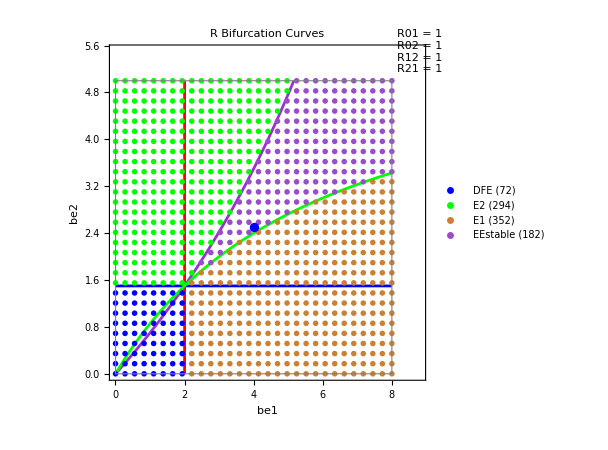

```mathematica
{plF,errors,res}=scanPar[RHS,var,par,p0val,plotInd,30,plot];plF
```

```mathematica
{plF,errors,res}=scanPar[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05];plot
```

Varying parameters at indices {1,2} with center values: {4,5/2}

Using range mode with step size 0.05...

Total points to scan: 16000

Scanning complete!

Found equilibrium types: {DFE (1200 points),E2 (5206 points),E1 (6379 points),EEstable (3215 points)}

Including 0 errors

Summary:

DFE | 1200 | 8%
E2 | 5206 | 33%
E1 | 6379 | 40%
EEstable | 3215 | 20%

-Graphics-

```mathematica
(*Fast parameter scanning using claP logic*)scanPar[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic]:=Module[{(*Parameter ranges and scanning*)β1,β2,β1min,β1max,β2min,β2max,stepSize,β1vals,β2vals,totalPoints,(*Results collection*)res,outcomes,outcomeCounts,(*Plotting and visualization*)finalPlot,plotData,betterColors,simpleTooltips,(*Mode detection*)useGridMode,β1Index,β2Index,β1Center,β2Center,(*Progress tracking*)progressVar,currentProgress,(*R curve variables*)R01F,R02F,R21F,R12F,rCurves,coPForR,(*Fast classification variables*)numpar,conPar,inP,sol,I1val,I2val,tol,currentType,errors,gridResults,nB1,nB2,jac,eigs,maxRealPart},(*Define better colors with old EE colors*)betterColors={RGBColor[0,0,1],(*Pure Blue for DFE*)RGBColor[0,1,0],(*Pure Green for E1*)RGBColor[0.8,0.5,0.2],(*Orange for E2*)RGBColor[0.6,0.3,0.8],(*Purple for EEstable*)RGBColor[1,0,0],(*Pure Red for EEunstable*)RGBColor[1.0,0.0,1.0](*Magenta for errors/NoSol*)};
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract parameter indices*)β1Index=If[Length[plotInd]>=1,plotInd[[1]],1];
β2Index=If[Length[plotInd]>=2,plotInd[[2]],2];
β1Center=p0val[[β1Index]];
β2Center=p0val[[β2Index]];
Print["Varying parameters at indices ",{β1Index,β2Index}," with center values: ",{β1Center,β2Center}];
If[useGridMode,(*GRID MODE*)Print["Using grid mode with ",gridRes,"×",gridRes," points..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1min+(β1max-β1min)*k/(gridRes-1),{k,0,gridRes-1}];
β2vals=Table[β2min+(β2max-β2min)*k/(gridRes-1),{k,0,gridRes-1}];
stepSize="grid";,(*RANGE MODE*)Print["Using range mode with step size ",delta,"..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1,{β1,β1min,β1max,delta}];
β2vals=Table[β2,{β2,β2min,β2max,delta}];
stepSize=delta;];
(*R curve preparation*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R21=!=Automatic||R12=!=Automatic,coPForR=Thread[par->p0val];
coPForR=DeleteCases[coPForR,HoldPattern[par[[β1Index]]->_]|HoldPattern[par[[β2Index]]->_]];
If[R01=!=Automatic,R01F=R01/. coPForR;
AppendTo[rCurves,ContourPlot[R01F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Red,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R02=!=Automatic,R02F=R02/. coPForR;
AppendTo[rCurves,ContourPlot[R02F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Blue,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R21=!=Automatic,R21F=R21/. coPForR;
AppendTo[rCurves,ContourPlot[R21F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Green,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R12=!=Automatic,R12F=R12/. coPForR;
AppendTo[rCurves,ContourPlot[R12F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Orange,Thick,Opacity[0.8]],PlotPoints->30]]];];
totalPoints=Length[β1vals]*Length[β2vals];
Print["Total points to scan: ",totalPoints];
(*Initialize for fast scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
inP=Table[{var[[j]],1/Length[var]},{j,Length[var]}];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[β1Index]]=β1;
numpar[[β2Index]]=β2;
conPar=Thread[par->numpar];
(*Single FindRoot call with equal initial conditions*)sol=Quiet[FindRoot[RHS/. conPar,inP]];
If[Head[sol]===List,(*Extract I1,I2 and classify*){I1val,I2val}={I1,I2}/. sol;
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,(*Both strains present-check EE stability*)(jac=D[RHS,{var}]/. conPar/. sol;
eigs=Chop[Eigenvalues[jac]//N];
maxRealPart=Max[Re[eigs]];
If[maxRealPart<0,"EEstable","EEunstable"])];
res=Append[res,{N[β1],N[β2],currentType}];,(*FindRoot failed*)res=Append[res,{N[β1],N[β2],"NoSol"}];];,{β2,β2vals}];,{β1,β1vals}];
Print["Scanning complete!"];
(*Simple error detection for grid mode*)errors={};
If[useGridMode&&gridRes>2,gridResults=Table[Table[Null,{j,1,gridRes}],{i,1,gridRes}];
Do[Do[pos=Position[res,{β1vals[[i]],β2vals[[j]],_}];
If[Length[pos]>0,gridResults[[i,j]]=res[[pos[[1,1]],3]]];,{j,1,gridRes}];,{i,1,gridRes}];
Do[Do[If[gridResults[[i,j]]=!=Null,neighbors={};
If[i>1,AppendTo[neighbors,gridResults[[i-1,j]]]];
If[i<gridRes,AppendTo[neighbors,gridResults[[i+1,j]]]];
If[j>1,AppendTo[neighbors,gridResults[[i,j-1]]]];
If[j<gridRes,AppendTo[neighbors,gridResults[[i,j+1]]]];
neighbors=DeleteCases[neighbors,Null];
If[Length[neighbors]>=3&&Length[DeleteDuplicates[Join[{gridResults[[i,j]]},neighbors]]]>=4,AppendTo[errors,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
pos=Position[res,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
If[Length[pos]>0,res[[pos[[1,1]],3]]="error"];];];,{j,2,gridRes-1}];,{i,2,gridRes-1}];];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
Print["Found equilibrium types: ",Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>" points)",{i,1,Length[outcomes]}]];
Print["Including ",Length[errors]," errors"];
(*Create plot*)simpleTooltips=Table[Table[If[res[[j,3]]==outcomes[[i]],Tooltip[res[[j,1;;2]],outcomes[[i]]<>": β1="<>ToString[Round[res[[j,1]],0.01]]<>", β2="<>ToString[Round[res[[j,2]],0.01]]],Nothing],{j,1,Length[res]}],{i,1,Length[outcomes]}];
finalPlot=ListPlot[simpleTooltips,GridLines->Automatic,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>")",{i,1,Length[outcomes]}],AspectRatio->1,PlotLabel->"Parameter Space Analysis ("<>ToString[Length[res]]<>" points)",FrameLabel->{"Parameter "<>ToString[β1Index],"Parameter "<>ToString[β2Index]},LabelStyle->{FontSize->12,Black},ImageSize->450,PlotRange->{{β1min,β1max},{β2min,β2max}}];
(*Add R curves and overlays*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot,Sequence@@rCurves,Graphics[{EdgeForm[{Thick,Gray,Dashed}],FaceForm[None],Rectangle[{β1min,β2min},{β1max,β2max}],Blue,PointSize[0.015],Point[{{β1Center,β2Center}}]}],PlotRange->{{β1min*0.9,β1max*1.1},{β2min*0.9,β2max*1.1}}];,If[Length[rCurves]>0,finalPlot=Show[finalPlot,Sequence@@rCurves];];];
Print[Style["Summary:",FontWeight->Bold]];
Print[Grid[Table[{outcomes[[i]],outcomeCounts[[i]],ToString[Round[100.*outcomeCounts[[i]]/Length[res],1]]<>"%"},{i,1,Length[outcomes]}],Frame->All,Alignment->Left]];
{finalPlot,errors,res}];

(*Grid mode:scanPar[RHS,var,par,p0val,{1,2},30,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12]*)
(*Range mode:scanPar[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05,1.0,1.0,R01,R02,R21,R12]*)
plotInd={1,2};coP
p0val=par/.coP
{ploF,errors,res}=scanPar[RHS,var,par,p0val,plotInd,10(*,plot,.01*)];ploF
```

```mathematica
(*EXECUTE THIS FIRST:*)Clear[scan4TS]

(*Time Series Simulation-based multiple equilibrium scanning*)
scan4TS[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic,tMax_:100,nInitials_:8,steadyTol_:10^(-6)]:=Block[{bifP1,bifP2,bifP1min,bifP1max,bifP2min,bifP2max,stepSize,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,betterColors,simpleTooltips,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,R01F,R02F,R21F,R12F,rCurves,coPForR,numpar,conPar,initialConditions,tsol,finalValues,I1val,I2val,tol,currentType,errors,gridResults,I1Index,I2Index,solTol,allSols,uniqueSols,eqType,eqTypes,steadyStateReached,lastValues,deltaCheck,icSet,ic,finalTime,pos,rhsWithParams,rhsWithFunctions,odeSystem,initialCondSystem},(*Define colors including detailed coexistence categories*)betterColors={RGBColor[0,0,1],(*Pure Blue for DFE*)RGBColor[0,1,0],(*Pure Green for E1*)RGBColor[0.8,0.5,0.2],(*Orange for E2*)RGBColor[0.6,0.3,0.8],(*Purple for EE*)RGBColor[1,1,0],(*Yellow for EE-E1*)RGBColor[1,0.5,0],(*Red-Orange for EE-E2*)RGBColor[0,0.8,0.8],(*Cyan for E1-E2*)RGBColor[0.8,0,0.8],(*Magenta for EE-DFE*)RGBColor[0.5,0.8,0.5],(*Light Green for E1-DFE*)RGBColor[0.8,0.8,0.5],(*Light Orange for E2-DFE*)RGBColor[1.0,0.0,1.0](*Magenta for errors/NoSol*)};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
Print["I1 at index ",I1Index,", I2 at index ",I2Index];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract bifurcation parameter indices from plotInd*)bifParIdx1=First[plotInd];
bifParIdx2=Last[plotInd];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
Print["Varying bifurcation parameters at indices ",{bifParIdx1,bifParIdx2}," with center values: ",{bifP1Center,bifP2Center}];
Print["Time series simulation: tMax = ",tMax,", steadyTol = ",steadyTol,", nInitials = ",nInitials];
If[useGridMode,(*GRID MODE*)Print["Using grid mode with ",gridRes,"×",gridRes," points..."];
bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];
stepSize="grid";,(*RANGE MODE*)Print["Using range mode with step size ",delta,"..."];
bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}];
stepSize=delta;];
(*R curve preparation*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R21=!=Automatic||R12=!=Automatic,coPForR=Thread[par->p0val];
coPForR=DeleteCases[coPForR,HoldPattern[Part[par,bifParIdx1]->_]|HoldPattern[Part[par,bifParIdx2]->_]];
If[R01=!=Automatic,R01F=R01/. coPForR;
AppendTo[rCurves,ContourPlot[R01F==1,{Part[par,bifParIdx1],bifP1min,bifP1max},{Part[par,bifParIdx2],bifP2min,bifP2max},ContourStyle->Directive[Red,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R02=!=Automatic,R02F=R02/. coPForR;
AppendTo[rCurves,ContourPlot[R02F==1,{Part[par,bifParIdx1],bifP1min,bifP1max},{Part[par,bifParIdx2],bifP2min,bifP2max},ContourStyle->Directive[Blue,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R21=!=Automatic,R21F=R21/. coPForR;
AppendTo[rCurves,ContourPlot[R21F==1,{Part[par,bifParIdx1],bifP1min,bifP1max},{Part[par,bifParIdx2],bifP2min,bifP2max},ContourStyle->Directive[Green,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R12=!=Automatic,R12F=R12/. coPForR;
AppendTo[rCurves,ContourPlot[R12F==1,{Part[par,bifParIdx1],bifP1min,bifP1max},{Part[par,bifParIdx2],bifP2min,bifP2max},ContourStyle->Directive[Orange,Thick,Opacity[0.8]],PlotPoints->30]]];];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
Print["Total points to scan: ",totalPoints];
(*Initialize for time series scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);(*Tolerance for comparing final states*)(*Create diverse initial condition sets*)initialConditions={};
(*Set 1:DFE-like (I1=I2≈0)*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 2:E1-like (I2≈0)*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 3:E2-like (I1≈0)*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Set 4:EE-like (both high)*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Additional random initial conditions*)Do[icSet=Table[RandomReal[{0.001,0.2}],{Length[var]}];
AppendTo[initialConditions,icSet];,{nInitials-4}];
Print["Created ",Length[initialConditions]," different initial conditions"];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP WITH TIME SERIES SIMULATION*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Substitute parameters in RHS*)rhsWithParams=RHS/. conPar;
(*Transform variables to functions of t:S->S[t],I1->I1[t],etc*)rhsWithFunctions=rhsWithParams/. Thread[var->Through[var[t]]];
(*Run time series from different initial conditions*)allSols={};
Do[ic=initialConditions[[k]];
(*Construct ODE system*)odeSystem=MapThread[#1'[t]==#2&,{var,rhsWithFunctions}];
initialCondSystem=MapThread[#1[0]==#2&,{var,ic}];
(*Solve ODE system*)tsol=Quiet[NDSolve[Join[odeSystem,initialCondSystem],var,{t,0,tMax}]];
If[Length[tsol]>0&&tsol[[1]]=!=$Failed,(*Extract final values*)finalValues=Table[var[[j]][tMax]/. tsol[[1]],{j,1,Length[var]}];
(*Check if steady state was reached*)finalTime=0.9*tMax;
lastValues=Table[var[[j]][finalTime]/. tsol[[1]],{j,1,Length[var]}];
deltaCheck=Max[Abs[finalValues-lastValues]];
steadyStateReached=(deltaCheck<steadyTol);
If[steadyStateReached&&AllTrue[finalValues,#>=0&],AppendTo[allSols,finalValues]];];,{k,1,Length[initialConditions]}];
If[Length[allSols]>0,(*Find unique attractors (within tolerance)*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify based on number of unique attractors*)If[Length[uniqueSols]>1,(*Multiple attractors-classify each and determine coexistence type*)eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
(*Remove duplicates and sort to get consistent naming*)eqTypes=Sort[DeleteDuplicates[eqTypes]];
(*Determine coexistence type*)currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",ContainsAll[eqTypes,{"EE","DFE"}]&&Length[eqTypes]==2,"EE-DFE",ContainsAll[eqTypes,{"E1","DFE"}]&&Length[eqTypes]==2,"E1-DFE",ContainsAll[eqTypes,{"E2","DFE"}]&&Length[eqTypes]==2,"E2-DFE",True,"3-4 Fps" (*For 3+types or unexpected combinations*)];,(*Single attractor-classify by I1,I2 values*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[bifP1],N[bifP2],currentType}];,(*No steady states found or all simulations failed*)res=Append[res,{N[bifP1],N[bifP2],"NoSol"}];];,{bifP2,bifP2vals}];,{bifP1,bifP1vals}];
Print["Time series scanning complete!"];
(*Simple error detection for grid mode*)errors={};
If[useGridMode&&gridRes>2,gridResults=Table[Table[Null,{j,1,gridRes}],{i,1,gridRes}];
Do[Do[pos=Position[res,{bifP1vals[[i]],bifP2vals[[j]],_}];
If[Length[pos]>0,gridResults[[i,j]]=res[[pos[[1,1]],3]]];,{j,1,gridRes}];,{i,1,gridRes}];
Do[Do[If[gridResults[[i,j]]=!=Null,neighbors={};
If[i>1,AppendTo[neighbors,gridResults[[i-1,j]]]];
If[i<gridRes,AppendTo[neighbors,gridResults[[i+1,j]]]];
If[j>1,AppendTo[neighbors,gridResults[[i,j-1]]]];
If[j<gridRes,AppendTo[neighbors,gridResults[[i,j+1]]]];
neighbors=DeleteCases[neighbors,Null];
If[Length[neighbors]>=3&&Length[DeleteDuplicates[Join[{gridResults[[i,j]]},neighbors]]]>=4,AppendTo[errors,{bifP1vals[[i]],bifP2vals[[j]],gridResults[[i,j]]}];
pos=Position[res,{bifP1vals[[i]],bifP2vals[[j]],gridResults[[i,j]]}];
If[Length[pos]>0,res[[pos[[1,1]],3]]="error"];];];,{j,2,gridRes-1}];,{i,2,gridRes-1}];];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
Print["Found equilibrium types: ",Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>" points)",{i,1,Length[outcomes]}]];
Print["Including ",Length[errors]," errors"];
(*Create plot*)simpleTooltips=Table[Table[If[res[[j,3]]==outcomes[[i]],Tooltip[res[[j,1;;2]],outcomes[[i]]<>": "<>ToString[Part[par,bifParIdx1]]<>"="<>ToString[Round[res[[j,1]],0.01]]<>", "<>ToString[Part[par,bifParIdx2]]<>"="<>ToString[Round[res[[j,2]],0.01]]],Nothing],{j,1,Length[res]}],{i,1,Length[outcomes]}];
finalPlot=ListPlot[simpleTooltips,GridLines->Automatic,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>")",{i,1,Length[outcomes]}],AspectRatio->1,PlotLabel->"Time Series Bifurcation Analysis ("<>ToString[Length[res]]<>" points)",FrameLabel->{ToString[Part[par,bifParIdx1]],ToString[Part[par,bifParIdx2]]},LabelStyle->{FontSize->12,Black},ImageSize->450,PlotRange->{{bifP1min,bifP1max},{bifP2min,bifP2max}}];
(*Add R curves and overlays*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot,Sequence@@rCurves,Graphics[{EdgeForm[{Thick,Gray,Dashed}],FaceForm[None],Rectangle[{bifP1min,bifP2min},{bifP1max,bifP2max}],Blue,PointSize[0.015],Point[{{bifP1Center,bifP2Center}}]}],PlotRange->{{bifP1min*0.9,bifP1max*1.1},{bifP2min*0.9,bifP2max*1.1}}];,If[Length[rCurves]>0,finalPlot=Show[finalPlot,Sequence@@rCurves];];];
Print[Style["Summary:",FontWeight->Bold]];
Print[Grid[Table[{outcomes[[i]],outcomeCounts[[i]],ToString[Round[100.*outcomeCounts[[i]]/Length[res],1]]<>"%"},{i,1,Length[outcomes]}],Frame->All,Alignment->Left]];
{finalPlot,errors,res}];

(*Usage:*)
(*plotInd={1,2};*)
(*scan4TS[RHS,var,par,p0val,plotInd,15,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12,100,8,10^(-6)]*)
```

I1 at index 2, I2 at index 5

Varying bifurcation parameters at indices {1,2} with center values: {4,5/2}

Time series simulation: tMax = 100, steadyTol = 1/1000000, nInitials = 8

Using grid mode with 15×15 points...

StringForm::sfr: Item 2 requested in "`1` cannot be interpreted. The operator `2` requires a subscript with a variable specification." out of range; 1 items available.

Internal`LocalizedBlock::novar: {be1,be2,et1,et2,ga1,ga2,La,mu,si1,si2,«3»}⟦bifParIdx1⟧ cannot be interpreted. The operator `2` requires a subscript with a variable specification.

StringForm::sfr: Item 2 requested in "`1` cannot be interpreted. The operator `2` requires a subscript with a variable specification." out of range; 1 items available.

Internal`LocalizedBlock::novar: {be1,be2,et1,et2,ga1,ga2,La,mu,si1,si2,«3»}⟦bifParIdx1⟧ cannot be interpreted. The operator `2` requires a subscript with a variable specification.

StringForm::sfr: Item 2 requested in "`1` cannot be interpreted. The operator `2` requires a subscript with a variable specification." out of range; 1 items available.

General::stop: Further output of StringForm::sfr will be suppressed during this calculation.

Internal`LocalizedBlock::novar: {be1,be2,et1,et2,ga1,ga2,La,mu,si1,si2,«3»}⟦bifParIdx1⟧ cannot be interpreted. The operator `2` requires a subscript with a variable specification.

General::stop: Further output of Internal`LocalizedBlock::novar will be suppressed during this calculation.

Total points to scan: 225

Created 8 different initial conditions

Time series scanning complete!

Found equilibrium types: {DFE (10 points),NoSol (36 points),E2 (65 points),error (1 points),E1 (79 points),EE (34 points)}

Including 1 errors

Show::gcomb: Could not combine the graphics objects in ….

Summary:

DFE | 10 | 4%
NoSol | 36 | 16%
E2 | 65 | 29%
error | 1 | 0%
E1 | 79 | 35%
EE | 34 | 15%

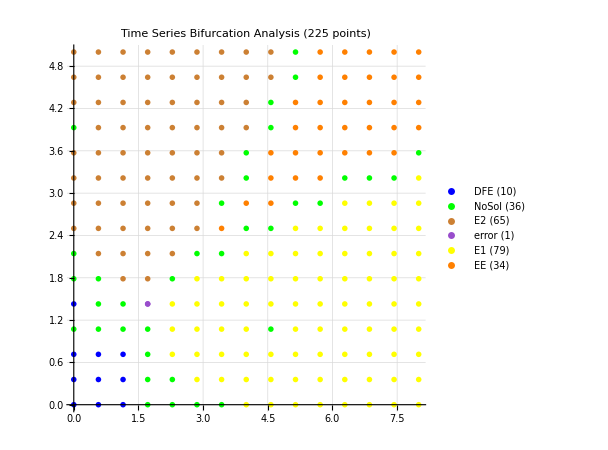
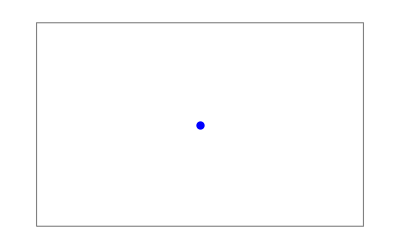
{Show[plot,-Graphics-,$Failed,$Failed,$Failed,$Failed,-Graphics-,PlotRange→{{0.0009,8.8},{0.0009,5.5}}],{{1.71507,1.42929,DFE}},{{0.001,0.001,DFE},{0.001,0.358071,DFE},{0.001,0.715143,DFE},{0.001,1.07221,NoSol},{0.001,1.42929,DFE},{0.001,1.78636,NoSol},{0.001,2.14343,NoSol},{0.001,2.5005,E2},{0.001,2.85757,E2},{0.001,3.21464,E2},{0.001,3.57171,E2},{0.001,3.92879,NoSol},{0.001,4.28586,E2},{0.001,4.64293,E2},{0.001,5.,E2},{0.572357,0.001,DFE},{0.572357,0.358071,DFE},{0.572357,0.715143,DFE},{0.572357,1.07221,NoSol},{0.572357,1.42929,NoSol},{0.572357,1.78636,NoSol},{0.572357,2.14343,E2},{0.572357,2.5005,E2},{0.572357,2.85757,E2},{0.572357,3.21464,E2},{0.572357,3.57171,E2},{0.572357,3.92879,E2},{0.572357,4.28586,E2},{0.572357,4.64293,E2},{0.572357,5.,E2},{1.14371,0.001,DFE},{1.14371,0.358071,DFE},{1.14371,0.715143,DFE},{1.14371,1.07221,NoSol},{1.14371,1.42929,NoSol},{1.14371,1.78636,E2},{1.14371,2.14343,E2},{1.14371,2.5005,E2},{1.14371,2.85757,E2},{1.14371,3.21464,E2},{1.14371,3.57171,E2},{1.14371,3.92879,E2},{1.14371,4.28586,E2},{1.14371,4.64293,E2},{1.14371,5.,E2},{1.71507,0.001,NoSol},{1.71507,0.358071,NoSol},{1.71507,0.715143,NoSol},{1.71507,1.07221,NoSol},{1.71507,1.42929,error},{1.71507,1.78636,E2},{1.71507,2.14343,E2},{1.71507,2.5005,E2},{1.71507,2.85757,E2},{1.71507,3.21464,E2},{1.71507,3.57171,E2},{1.71507,3.92879,E2},{1.71507,4.28586,E2},{1.71507,4.64293,E2},{1.71507,5.,E2},{2.28643,0.001,NoSol},{2.28643,0.358071,NoSol},{2.28643,0.715143,E1},{2.28643,1.07221,E1},{2.28643,1.42929,E1},{2.28643,1.78636,NoSol},{2.28643,2.14343,E2},{2.28643,2.5005,E2},{2.28643,2.85757,E2},{2.28643,3.21464,E2},{2.28643,3.57171,E2},{2.28643,3.92879,E2},{2.28643,4.28586,E2},{2.28643,4.64293,E2},{2.28643,5.,E2},{2.85779,0.001,NoSol},{2.85779,0.358071,E1},{2.85779,0.715143,E1},{2.85779,1.07221,E1},{2.85779,1.42929,E1},{2.85779,1.78636,E1},{2.85779,2.14343,NoSol},{2.85779,2.5005,E2},{2.85779,2.85757,E2},{2.85779,3.21464,E2},{2.85779,3.57171,E2},{2.85779,3.92879,E2},{2.85779,4.28586,E2},{2.85779,4.64293,E2},{2.85779,5.,E2},{3.42914,0.001,NoSol},{3.42914,0.358071,E1},{3.42914,0.715143,E1},{3.42914,1.07221,E1},{3.42914,1.42929,E1},{3.42914,1.78636,E1},{3.42914,2.14343,NoSol},{3.42914,2.5005,EE},{3.42914,2.85757,NoSol},{3.42914,3.21464,E2},{3.42914,3.57171,E2},{3.42914,3.92879,E2},{3.42914,4.28586,E2},{3.42914,4.64293,E2},{3.42914,5.,E2},{4.0005,0.001,E1},{4.0005,0.358071,E1},{4.0005,0.715143,E1},{4.0005,1.07221,E1},{4.0005,1.42929,E1},{4.0005,1.78636,E1},{4.0005,2.14343,E1},{4.0005,2.5005,NoSol},{4.0005,2.85757,EE},{4.0005,3.21464,NoSol},{4.0005,3.57171,NoSol},{4.0005,3.92879,E2},{4.0005,4.28586,E2},{4.0005,4.64293,E2},{4.0005,5.,E2},{4.57186,0.001,E1},{4.57186,0.358071,E1},{4.57186,0.715143,E1},{4.57186,1.07221,NoSol},{4.57186,1.42929,E1},{4.57186,1.78636,E1},{4.57186,2.14343,E1},{4.57186,2.5005,NoSol},{4.57186,2.85757,EE},{4.57186,3.21464,EE},{4.57186,3.57171,EE},{4.57186,3.92879,NoSol},{4.57186,4.28586,NoSol},{4.57186,4.64293,E2},{4.57186,5.,E2},{5.14321,0.001,E1},{5.14321,0.358071,E1},{5.14321,0.715143,E1},{5.14321,1.07221,E1},{5.14321,1.42929,E1},{5.14321,1.78636,E1},{5.14321,2.14343,E1},{5.14321,2.5005,E1},{5.14321,2.85757,NoSol},{5.14321,3.21464,EE},{5.14321,3.57171,EE},{5.14321,3.92879,EE},{5.14321,4.28586,EE},{5.14321,4.64293,NoSol},{5.14321,5.,NoSol},{5.71457,0.001,E1},{5.71457,0.358071,E1},{5.71457,0.715143,E1},{5.71457,1.07221,E1},{5.71457,1.42929,E1},{5.71457,1.78636,E1},{5.71457,2.14343,E1},{5.71457,2.5005,E1},{5.71457,2.85757,NoSol},{5.71457,3.21464,EE},{5.71457,3.57171,EE},{5.71457,3.92879,EE},{5.71457,4.28586,EE},{5.71457,4.64293,EE},{5.71457,5.,EE},{6.28593,0.001,E1},{6.28593,0.358071,E1},{6.28593,0.715143,E1},{6.28593,1.07221,E1},{6.28593,1.42929,E1},{6.28593,1.78636,E1},{6.28593,2.14343,E1},{6.28593,2.5005,E1},{6.28593,2.85757,E1},{6.28593,3.21464,NoSol},{6.28593,3.57171,EE},{6.28593,3.92879,EE},{6.28593,4.28586,EE},{6.28593,4.64293,EE},{6.28593,5.,EE},{6.85729,0.001,E1},{6.85729,0.358071,E1},{6.85729,0.715143,E1},{6.85729,1.07221,E1},{6.85729,1.42929,E1},{6.85729,1.78636,E1},{6.85729,2.14343,E1},{6.85729,2.5005,E1},{6.85729,2.85757,E1},{6.85729,3.21464,NoSol},{6.85729,3.57171,EE},{6.85729,3.92879,EE},{6.85729,4.28586,EE},{6.85729,4.64293,EE},{6.85729,5.,EE},{7.42864,0.001,E1},{7.42864,0.358071,E1},{7.42864,0.715143,E1},{7.42864,1.07221,E1},{7.42864,1.42929,E1},{7.42864,1.78636,E1},{7.42864,2.14343,E1},{7.42864,2.5005,E1},{7.42864,2.85757,E1},{7.42864,3.21464,NoSol},{7.42864,3.57171,EE},{7.42864,3.92879,EE},{7.42864,4.28586,EE},{7.42864,4.64293,EE},{7.42864,5.,EE},{8.,0.001,E1},{8.,0.358071,E1},{8.,0.715143,E1},{8.,1.07221,E1},{8.,1.42929,E1},{8.,1.78636,E1},{8.,2.14343,E1},{8.,2.5005,E1},{8.,2.85757,E1},{8.,3.21464,E1},{8.,3.57171,NoSol},{8.,3.92879,EE},{8.,4.28586,EE},{8.,4.64293,EE},{8.,5.,EE}}}

```mathematica
plotInd={1,2};
scan4TS[RHS,var,par,p0val,plotInd,15,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12,100,8,10^(-6)]
```

```mathematica
Clear[scan]
(*Equilibrium scanning with R-curve plotting*)scan[RHS_,var_,par_,p0val_,plotInd_,varInd_,gridRes_:Automatic,plot_:Automatic,steadyTol_:10^(-5),stabTol_:10^(-8),chopTol_:10^(-10),R01_:Automatic,R02_:Automatic,R12_:Automatic,R21_:Automatic]:=Block[{bifP1min,bifP1max,bifP2min,bifP2max,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,numpar,conPar,delta,wRan,hRan,eq,EE,E1,E2,DFE,eigs,complexEigs,realParts,jac,rCurves,fixedParams,fInd,activeEquations,activeColors,activeLabels,par1,par2,range1,range2,varS,varI1,varI2,zeroTol,posTol},(*Set default step_size scanning parameters*)delta=1/10;
wRan=1;
hRan=1;
(*Extract variable indices for equilibrium classification*)If[Length[varInd]!=3,Print["Error: varInd must contain exactly 3 indices for [S, I1, I2]"];
Return[$Failed]];
varS=var[[varInd[[1]]]];(*Susceptible variable*)varI1=var[[varInd[[2]]]];(*Strain 1 variable*)varI2=var[[varInd[[3]]]];(*Strain 2 variable*)(*Fixed color mapping*)colorMap=<|"DFE"->RGBColor[0,0,1],"E1"->RGBColor[0,1,0],"E2"->RGBColor[0.6,0.2,0.8],"EE-Stable"->RGBColor[1,1,0],"EE-Unstable"->RGBColor[0.9,0.4,0.4],"NoSol"->RGBColor[1,0,0]|>;
(*Extract bifurcation parameter indices for plotting*)If[Length[plotInd]!=2,Print["Error: plotInd must contain exactly 2 indices for plotting"];
Return[$Failed]];
bifParIdx1=plotInd[[1]];
bifParIdx2=plotInd[[2]];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
(*Parameters for R-curve plotting*)par1=par[[bifParIdx1]];
par2=par[[bifParIdx2]];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Set parameter ranges and values*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
range1={bifP1min,bifP1max};
range2={bifP2min,bifP2max};
If[useGridMode,(*GRID MODE*)bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];,(*RANGE MODE*)bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}]];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
(*Initialize for scanning*)res={};
currentProgress=0;
progressVar=0;
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Solve equilibrium system with numerical precision*)eq=Quiet[N[Solve[Join[Thread[(RHS/. conPar)==0],Thread[var>=0]],var]],Solve::ratnz];
(*Define tolerance for numerical zeros*)zeroTol=10^(-10);
posTol=10^(-8);
(*Classify equilibrium types using specified variable indices*)EE=Select[eq,(varS/. #)>posTol&&(varI1/. #)>posTol&&(varI2/. #)>posTol&];
E1=Select[eq,(varS/. #)>posTol&&(varI1/. #)>posTol&&Abs[varI2/. #]<zeroTol&];
E2=Select[eq,(varS/. #)>posTol&&Abs[varI1/. #]<zeroTol&&(varI2/. #)>posTol&];
DFE=Select[eq,(varS/. #)>posTol&&Abs[varI1/. #]<zeroTol&&Abs[varI2/. #]<zeroTol&];
(*Handle equilibrium classification with explicit logic*)If[Length[EE]>=1,(*Found EE-check stability*)jac=D[RHS,{var}]/. conPar/. EE[[1]];
eigs=Chop[Eigenvalues[jac]//N,chopTol];
complexEigs=Select[eigs,Im[#]!=0&];
realParts=Re[complexEigs];
If[Length[complexEigs]>=2,If[Max[realParts]<0.,res=Append[res,{N[bifP1],N[bifP2],"EE-Stable"}],res=Append[res,{N[bifP1],N[bifP2],"EE-Unstable"}]],res=Append[res,{N[bifP1],N[bifP2],"EE-Stable"}]],(*No EE-check single strain equilibria*)If[Length[E1]>=1&&Length[E2]>=1,(*Both E1 and E2 exist-competitive exclusion zone*)If[bifP1>=bifP2,res=Append[res,{N[bifP1],N[bifP2],"E1"}],res=Append[res,{N[bifP1],N[bifP2],"E2"}]],(*Only one strain survives*)If[Length[E1]>=1,res=Append[res,{N[bifP1],N[bifP2],"E1"}],If[Length[E2]>=1,res=Append[res,{N[bifP1],N[bifP2],"E2"}],If[Length[DFE]>=1,res=Append[res,{N[bifP1],N[bifP2],"DFE"}],res=Append[res,{N[bifP1],N[bifP2],"NoSol"}]]]]]];,{bifP2,bifP2vals}],{bifP1,bifP1vals}];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
(*Create plot with fixed colors*)plotData=Table[Select[res,#[[3]]==outcomes[[i]]&][[All,1;;2]],{i,1,Length[outcomes]}];
plotMarkers=Table[{Style["■",colorMap[outcomes[[i]]]],12},{i,1,Length[outcomes]}];
finalPlot=ListPlot[plotData,PlotMarkers->plotMarkers,PlotLegends->outcomes,AspectRatio->1,PlotRange->{range1,range2},GridLines->Automatic];
(*Create R-curve plots*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R12=!=Automatic||R21=!=Automatic,fInd=Complement[Range[Length[par]],plotInd];
fixedParams=Thread[par[[fInd]]->p0val[[fInd]]];
activeEquations={};
activeColors={};
If[R01=!=Automatic,AppendTo[activeEquations,Evaluate[(R01/. fixedParams)==1]];
AppendTo[activeColors,Directive[Red,Thick]];];
If[R02=!=Automatic,AppendTo[activeEquations,Evaluate[(R02/. fixedParams)==1]];
AppendTo[activeColors,Directive[Blue,Thick]];];
If[R12=!=Automatic,AppendTo[activeEquations,Evaluate[(R12/. fixedParams)==1]];
AppendTo[activeColors,Directive[Purple,Thick]];];
If[R21=!=Automatic,AppendTo[activeEquations,Evaluate[(R21/. fixedParams)==1]];
AppendTo[activeColors,Directive[Green,Thick]];];
If[Length[activeEquations]>0,rCurves={ContourPlot[Evaluate[activeEquations],Evaluate[{par1,range1[[1]],range1[[2]]}],Evaluate[{par2,range2[[1]],range2[[2]]}],ContourStyle->activeColors,PlotPoints->50]};];];
(*Combine plots*)If[Length[rCurves]>0,finalPlot=Show[finalPlot,rCurves[[1]],Frame->True,FrameLabel->{ToString[par1],ToString[par2]},PlotLabel->"Equilibrium Classification with R-curves",ImageSize->450];,finalPlot=Show[finalPlot,Frame->True,FrameLabel->{ToString[par1],ToString[par2]},PlotLabel->"Equilibrium Classification",ImageSize->450];];
(*Simple summary with percentages*)Do[Print[outcomes[[i]],": ",outcomeCounts[[i]]," (",Round[100.*outcomeCounts[[i]]/Length[res]],"%)"],{i,1,Length[outcomes]}];
(*Return NoSol points as errors*)noSolPoints=Select[res,#[[3]]=="NoSol"&];
{finalPlot,noSolPoints,res}];
varInd={1,2,3};steTol=10^(-8);staTol=10^(-10);choTol=10^(-13);(*tMax=300;nIc=8;*)
Timing[{fPl,unC,res}=scan[RHS,var,par,p0val,plotInd,varInd,Automatic,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]
fPl
```